```mathematica
num=10;
a=1;
b=0.5;
c=10;
d=10;
```

```mathematica
(*s=Array[(c-d)/n&,n]*)
s=Array[0&,num];
diag=Array[-(2a+b)-s[[#]]&,num];
diag[[1]]=-(a+b)-s[[1]];
diag[[num]]=-a-d-s[[num]];
α1=SparseArray[{
Band[{2,1}]->(a+b),
Band[{1,1}]->diag,
Band[{1,2}]->a
},{num,num}];
α1=Normal[α1];
α2=SparseArray[{
Band[{2,1}]->(a+b),
Band[{1,1}]->-diag,
Band[{1,2}]->a
},{num,num}];
α2=Normal[α2];
(*MatrixForm[α1]
MatrixForm[α2]*)
```

```mathematica
β1=Array[0&,num];
β1[[1]]=c;
β2=Array[0&,num];
β2[[1]]=c;
```

```mathematica
ClearAll[expn,expectation,expsystem,expinit]
```

```mathematica
expns[t_]:=Table[expn[i][t],{i,1,num}]
```

```mathematica
expsystem=D[expns[t],t]==α1.expns[t]+β1;
expns0=Array[0&,num];
(*Y0[[1]]=1000;*)
(*Y0[[n]]=0;*)
expinit=expns[0]==expns0;
```

```mathematica
expectation=NDSolveValue[{expsystem,expinit},expns[t],{t,0,500},PrecisionGoal->100];
expectationfunc[t0_]:=expectation/.t->t0
```

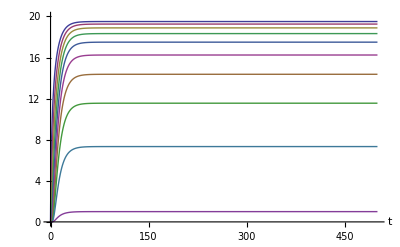

```mathematica
p=Plot[Evaluate[expectationfunc[t]],{t,0,500},AxesLabel->{t,Automatic},PlotRange->{0,20}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mrussell/phd/agent_based/gillespie

```mathematica
Export["exp.pdf",p]
```

exp.pdf

```mathematica
expdata=Table[Join[{t},expectationfunc[t]],{t,0,50,0.05}];
```

```mathematica
Export["exp.dat",expdata,"Table","FieldSeparators"->" "]
```

exp.dat

```mathematica
(*ClearAll[Z,variance,varsystem,varinit]*)
```

```mathematica
(*Zs[t_]:=Table[Z[i][t],{i,1,n}]*)
```

```mathematica
(*varsystem=D[Zs[t],t]==A2.expectationfunc[t]+v2+2 DiagonalMatrix[diag].Zs[t];
Z0=Array[0&,n];
(*Y0[[1]]=1000;*)
(*Y0[[n]]=0;*)
varinit=Zs[0]==Z0;*)
```

```mathematica
(*sol=DSolve[{system,init},Ys[t],t];*)
```

```mathematica
(*variance=NDSolveValue[{varsystem,varinit},Zs[t],{t,0,500}];
variancefunc[t0_]:=variance/.t->t0*)
```

```mathematica
(*p=Plot[Evaluate[variancefunc[t]],{t,0,100},AxesLabel->{t,Automatic},PlotRange->Full]*)
```

```mathematica
(*vardata=Table[Join[{t},variancefunc[t]],{t,0,40,0.05}];*)
```

```mathematica
(*Export["var.dat",vardata,"Table","FieldSeparators"->" "]*)
```

```mathematica
a1mel[i_,j_,n_,s_,t_]:=Module[
{nf=Append[n,0]},
(a+b)(1-KroneckerDelta[i,1])(KroneckerDelta[i,j]-KroneckerDelta[i,j+1])n[[i-1]]+
(a(1-KroneckerDelta[i,1])(KroneckerDelta[i,j]-KroneckerDelta[i,j+1])+(a+b)(1-KroneckerDelta[i,num])(KroneckerDelta[i,j]-KroneckerDelta[i+1,j])+KroneckerDelta[i,j]s[[i]])n[[i]]+
a(1-KroneckerDelta[i,num])(KroneckerDelta[i,j]-KroneckerDelta[i+1,j])nf[[i+1]]+
KroneckerDelta[i,1]KroneckerDelta[j,1]c+
KroneckerDelta[i,num]KroneckerDelta[j,num]d n[[num]]
]
```

```mathematica
a1m[t_]:=Table[a1mel[i,j,expectationfunc[t],s,t],{i,1,num},{j,1,num}]
```

```mathematica
covs[t_]:=Table[cov[i][j][t],{i,1,num},{j,1,num}]
```

```mathematica
m[t_]:=α1.covs[t]
```

```mathematica
covsystem=D[covs[t],t]==a1m[t]+m[t]+Transpose[m[t]];
covs0=Table[0,{i,1,num},{j,1,num}];
```

```mathematica
covinit=covs[0]==covs0;
```

```mathematica
covariance=NDSolveValue[{covsystem,covinit},covs[t],{t,0,500},PrecisionGoal->100];
covariancefunc[t0_]:=covariance/.t->t0
```

```mathematica
Manipulate[ArrayPlot[covariancefunc[t],PlotRange->{0,100}],{t,0,50}]
```

```mathematica
Manipulate[covariancefunc[t]//MatrixForm,{t,0,500}]
```

```mathematica
covdata=covariancefunc[40];
```

```mathematica
Export["cov.dat",covdata,"FieldSeparators"->" "]
```

cov.dat